la función Plus[x,y,...] suma

la función Subtract[x,y] resta

la funciono Minus[x] cambia el signo

la función Times[x,y,...] multiplica

la función Divide[x,y] divide

para elevar usamos ctrl+6 aunque podemos usar la funcion Power[x,y] donde se eleva x a la y

para pasar un decimal a racional usamos la función Rationalize[y.udhd] 

NOTA: % le dice al programa que use el resultado anterior

podemos usar la función N[x/y, t] aqui ponemos una operacion y le damos el numero de cifras que queremos (aqui nos da t cifras)

la función Sqrt[] da la raiz cuadrada

para otras raices usamos la función Surd[2,5] por ejemplo y nos dara la quinta raiz de 2

nota: las funciones se escriben en mayúscula, entre corchetes y los argumentos se separan con comas

para redondear usamos Round[3.6] y te da el mas cercano (4),  Floor[3.6] da el mas cercano a la baja en este caso 3, Ceiling[3.6] redondea al mayor mas cercano en este caso 4

La funcion IntegerPart[3.6] nos da la parte entera (3) 

La funcion FraccionalPart[3.6] nos da la parte decimal (0.6)

para funciones trigonometricas en grados multiplicamos por Degree asi “Cos[60* Degree]


la funcion Log[x,y] es el logaritmo base x de y

para definir una funcion “g[x_,y_]:=   “ en este caso es de dod variables

## división con resto

cuando una dicion no es exacta esta tiene un residuo, por ejemplo 7/4 lo que mas se acerca es 4*1  lo que da 4 y se le suma un 3, que es el residuo, asi 

Quotient[7,4] te dara el 1

Mod[7,4] te dara 3

QuotientRemainder[7,4] te dara ambos {1,3}.

## otras

para saber si un numero es o no primo usamos 
PrimeQ[x]

Mathematica cuenta con una “lista” de primos, pra saber el que esta en cad posicion usamos 
Prime[x] y te da el primo numero x

PrimePi[x] te da el numero de primeros menores que x

FactorInteger[x] descompone x en factores primos

Divisors[x] te da los divisores de x

Maximo comun divisor de x,y,... es GCD[x,y,...]

Minimo comun divisor de x,y,... es LCM[x,y,...]

## polinomios

para desarrollar un polinomio usamos
Expand[aquí el polinomio]

para dividir polinomios con resto, podemos usar 
PolynomialQuotient[polinomio dividendo, polinomio divisor, variable generalmente x]

este nos dará la división, para el resto lo que  hacemos es 
PolynomialRemainder[polinomio dividendo, polinomio divisor, variable generalmente x]

y si queremos que nos de los dos juntos usamos
PolynomialQuotientRemainder[polinomio dividendo, polinomio divisor, variable generalmente x]

para factorizar polinomios usamos
Factor[polinomio]

En el caso de que para factorizar se necesiten complejos usamos
Factor[polinomio,GaussianIntegers→True]

Para calcular máximo común divisor y minino común múltiplo de polinomios 
PolynomialGCD[polinomio1, polinomio2,...]
y
PolynomialLCM[polinomio1, polinomio2,...]

Para darle valor a un polinomio lo que hacemos es definir el polinomio
f = polinomio
f / . x → numero
(sin espacios en el ultimo, claro)

para hacer la flecha hacemos -> y espacio

Para encontrar raices usamos
Roots[polinomio = = 0, variable]

si usamos
NRoots[ polinomio = = 0, variable, PrecisionGoal → y]
nos da las raíces en decimales con y cifras significativas

Para encontrar la ecuación del polinomio que pasa por ciertos puntos usamos
InterpolatingPolynomial[{{x1,y1},...,{xn.yn}}, variable a usar]

un polinomio mínimo de un numero (real o complejo) es el polinomio de menor grado que existe que tiene a ese numero como solución 
MinimalPolynomial[numero, variable]

```mathematica
o=(6-5 x+x^2)/(-2+x)
```

(6-5 x+x^2)/(-2+x)

```mathematica
Expand[o]
```

6/(-2+x)-(5 x)/(-2+x)+x^2/(-2+x)

```mathematica
Simplify[6/(-2+x)-(5 x)/(-2+x)+x^2/(-2+x)]
```

-3+x

## Ecuaciones y Sistemas

para resolver una sola ecuacion, usamos el comando
Solve[ecuacion = = resultado,variable a resolver]


si queremos la solucion en decimales  con k cifras usamos
NSolve[ecuacion = = resultado,variable a resolver, WorkingPrecision → k]

Para un sistema de k ecuaciones y k variables usamos
Solve[{ecuacion1 = = resultado1,...,ecuacionK = = resultadoK},{x,y,...,k}]

```mathematica
Solve[{x+y==9,2x+2y==18},{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→9-x}}

podemos ver como en el caso anterior hay infinitas soluciones, por defecto lo resuelve asi, pero si quieres puedes especificar en que variable se desea despejar poniendo solo dicha variable al final y no todas


cuando las ecuaciones no son algebraicas, la funcion solve no suele servir, asi lo que hacemos es usar, por ejemplo para la siguiente ecuación, el comando

```mathematica
FindRoot[Cos[x^2]-6x==Tan[x],{x,0}]
```

{x→0.142688}

```mathematica
FindRoot[{y==Exp[x],x+y==2},{{x,1},{y,2}}]
```

{x→0.442854,y→1.55715}

Como aquí hay muchas soluciones, le damos una “semilla” en este caso 0 y luego 1 y 2, que es al rededor del punto al cual se aproxima

#### Inecuaciones

Para las inecuaciones no usamos el comando solve, para esto usamos, para esta inecuacion .b4por ejemplo, el comando

```mathematica
Reduce[x^2-5x+6≥ 0,x]
```

x≤2||x≥3

para hacer menor o igual ponemos <= y damos espacio

## Numeros Complejos

La unidad imaginaria i se escribe como 
I (i mayuscula)


Para escribir un numero complejo tenemos dos opciones, podemos simplememte, por ejemplo

```mathematica
3+4I
```

```mathematica
3+4 ⅈ
```

o podemos usar el comando

```mathematica
Complex[3,4]
```

3+4 ⅈ

```mathematica
"convert to exponential"3+4 ⅈWith[{n=Abs[3+4 ⅈ],a=Arg[3+4 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

para encontrar el modulo de un complejo

```mathematica
Abs[3+4I]
```

5

para enontrar el argumento (angulo en radianes) de un complejo

```mathematica
Arg[3+4I ]
```

ArcTan[4/3]

```mathematica
N[ArcTan[4/3]]
```

0.927295

el conjugado de un complejo es

```mathematica
Conjugate[3+4I]
```

3-4 ⅈ

Para ver la parte real de un complejo

```mathematica
Re[3+4I]
```

3

Para ver la parte imaginaria

```mathematica
Im[3+4I]
```

4

Para que en una ecucacion te de las soluciones complejas usamos, por ejemplo

```mathematica
Solve[x^3-(-8)==0,x]//ComplexExpand
```

{{x→-2},{x→1+ⅈ √3},{x→1-ⅈ √3}}

## Graficar

Para esto usamos, por ejemplo

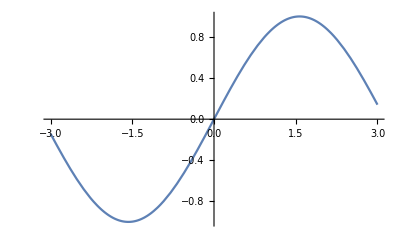

```mathematica
Plot[Sin[x],{x,-3,3}]
```

donde la segunda es el dominio de la grafica


para superponer funciones, las escribimos como una lista

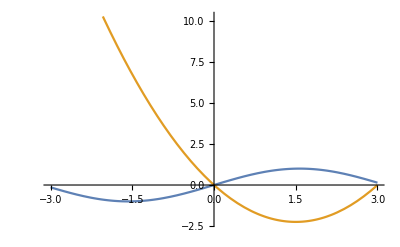

```mathematica
Plot[{Sin[x],x^2-3x},{x,-3,3}]
```

para ver todas las opciones que se puede usar en una grafica, usamos

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

veamos alguna

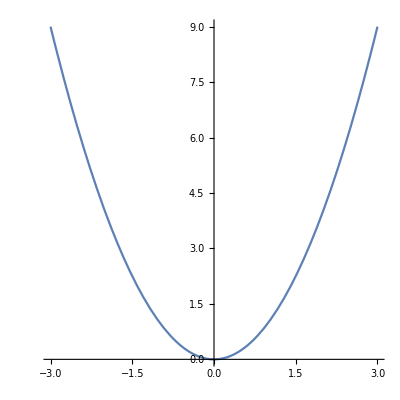

```mathematica
Plot[x^2,{x,-3,3},AspectRatio->1]
```

aspectradio te permite achatar o alargar la grafica, en 1 es un cuadrado, para igual tamaño de los 
ejes usamos Automatic

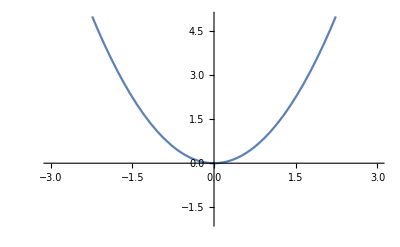

```mathematica
Plot[x^2,{x,-3,3},PlotRange->{-2,5}]
```

PlotRange es el rango de la funcion

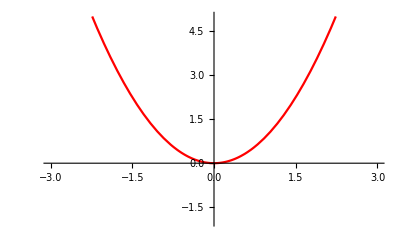

```mathematica
Plot[x^2,{x,-3,3},PlotRange->{-2,5},PlotStyle->Red]
```

Plotstyle te permite cambiar el color 




para graficar una funcion a trozos, hacmos lo siguiente

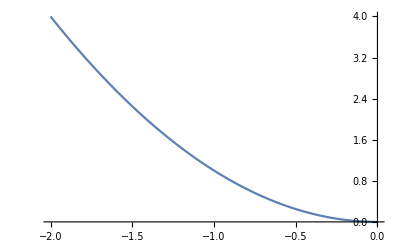

```mathematica
a=Plot [x^2,{x,-2,0}]
```

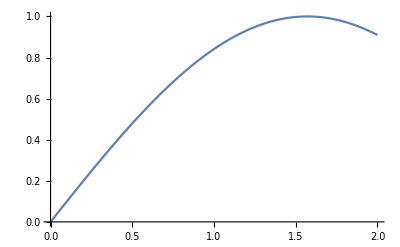

```mathematica
b=Plot[Sin[x],{x,0,2}]
```

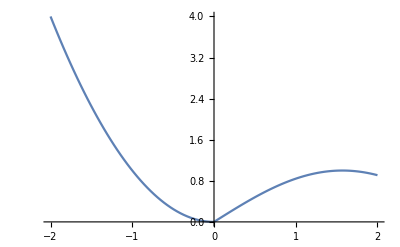

```mathematica
Show[a,b, PlotRange-> All]
```

debemos especificar que el rango es completo

otra manera es usando

```mathematica
f[x_]:=Piecewise[{{x^2,-2<x≤ 0},{Sin[x],0<x<2}}]
```

```mathematica
Plot[f,x]
```

Plot::pllim: Range specification x is not of the form {x, xmin, xmax}.

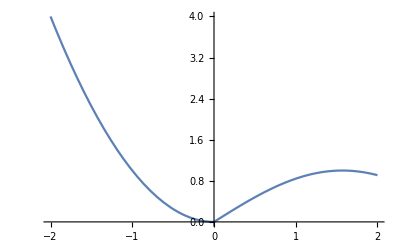

```mathematica
Plot[f[x],{x,-2,2}]
```

para funciones implicitas usamos

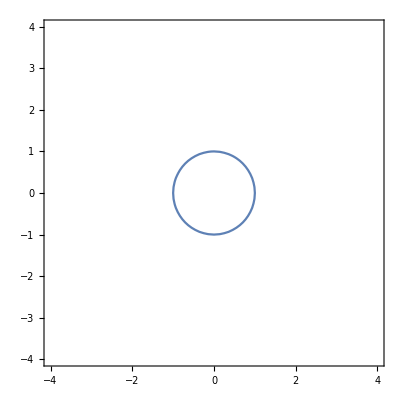

```mathematica
ContourPlot[x^2+y^2==1,{x,-4,4},{y,-4,4},Axes->True]
```

## limites

para calcular un limite, usamos

```mathematica
t[x_]:=Sin[x]/x
```

```mathematica
Limit[t[x],x-> 0]
```

1

sin embargo veamos que

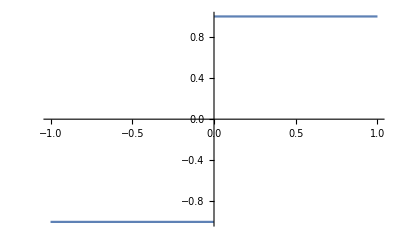

```mathematica
Plot[Abs[x]/x,{x,-1,1}]
```

y si calculamos su limite

```mathematica
Limit[Abs[x]/x,x->  0]
```

Indeterminate

si queremos especificar la direccion

```mathematica
Limit[Abs[x]/x,x->  0,Direction->-1]
```

1

donde -1 significa por derecha y 1 por izquierda

Para saber si la funcion tiene una asintota oblicua, que es en la cual la funcion tiende a una recta tipo mx+n, lo que hacemos es la siguiente

```mathematica
r[x_]:=(2 x^2-6x+3)/(x-4)
```

Para saber la pendiente m vemos que

```mathematica
m= Limit[r[x]/x,x-> Infinity]
```

2

y vemos que, en efecto, el limite existe, ahora buscamos n, o sea el termino independiente

```mathematica
Limit[r[x]-(m*x),x-> Infinity]
```

2

y podemos verlo en la grafica

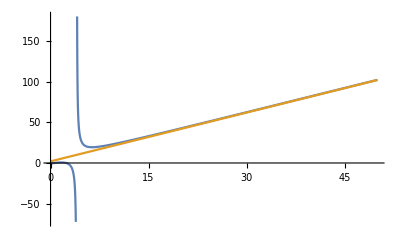

```mathematica
Plot[{r[x],2x+2},{x,0,50}]
```

## Derivadas

Para derivar usamos

```mathematica
D[3 x^2+8x,x]
```

8+6 x

el segundo argumento indica con respecto a que variable queremos derivar

```mathematica
D[Cos[y*x^2],y]
```

-x^2 Sin[x^2 y]

tenemos una manera mas sencilla de hacerlo y es usando la notacion prima

```mathematica
h[x_]:=3 x^2+8x
```

```mathematica
h'[x]
```

8+6 x

para hacer derivadas de orden superior usamos

```mathematica
D[Sin[6x],{x,5}]
```

7776 Cos[6 x]

donde el 5 representa el orden de la derivada, para ver lo que hacemos podemos usar

```mathematica
D[Sin[6x],{x,5}]//HoldForm
```

∂_{x,5} Sin[6 x]

si lo que queremos es derivar con respecto a las dos variables, lo que hacemos es

```mathematica
D[Sin[4x+6y],{x,2},{y,6}]
```

746496 Sin[4 x+6 y]

donde primero deriva dos veces con respecto a x y luego 6 en y

## Series de potencia

Para calcular la serie de potencia usamos

```mathematica
Series[Exp[x],{x,0,7}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+O[x]^8

la función, la variable, el punto al rededor , el numero de veces.
nota que aquí nos da el resto, para evitarlo usamos

```mathematica
Normal[Series[Exp[x],{x,0,7}]]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040

## Integrales

Para integrar usamos el comando

```mathematica
Integrate[x^5+3y,x]
```

x^6/6+3 x y

aqui es con respecto a x

para integrales definidas

```mathematica
Integrate[4 x^3+5,{x,0,4}]
```

276

que es la integral de 0 a 4 de esa funcion

Cuando tenemos una integral definida cuya antiderivada no existe, podemos decirle a mathematica que lo haga por metodos numericos

```mathematica
Integrate[Sin[x]/x,{x,0,4}]
```

```mathematica
SinIntegral[4]
```

```mathematica
NIntegrate[Sin[x]/x,{x,0,4}]
```

1.7582

si lo queremos con mas Precision

```mathematica
NIntegrate[Sin[x]/x,{x,0,4}, WorkingPrecision->20]
```

1.7582031389490530581

para descomponer en fracciones parciales usamos

```mathematica
Apart[(5x+3)/(x^2+2x-3)]
```

2/(-1+x)+3/(3+x)

## sumatorias

para calcular sumatorias (o series incluso) usamos este comando

```mathematica
Sum[n,{n,1,100}]
```

5050

le das la expresion a sumar, luego con respecto a que variable, y por ultimo de donde a donde

```mathematica
Sum[i^2,{i,1,n}]
```

1/6 n (1+n) (1+2 n)

para series (que va hasta infinito) no necesitamos usar el limite, solo lo ponemos como sigue

```mathematica
Sum[1/n^2,{n,1,Infinity}]
```

π^2/6

## Vectores

estos se escriben en forma de lista, o sea entre llaves

```mathematica
u={3,5,2}
```

{3,5,2}

```mathematica
v={8,4,9}
```

{8,4,9}

```mathematica
u+v
```

{11,9,11}

para dibujar vectores, primero lo definimos, diciendo de que punto a que punto va, esto se ponen en una lista asi

```mathematica
Arrow[{{0,0},{3,2}}]
```

Arrow[{{0,0},{3,2}}]

ahora lo graficamos

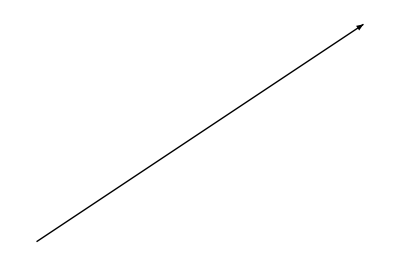

```mathematica
Graphics[Arrow[{{0,0},{3,2}}]]
```

pero para que aparezcan los ejes

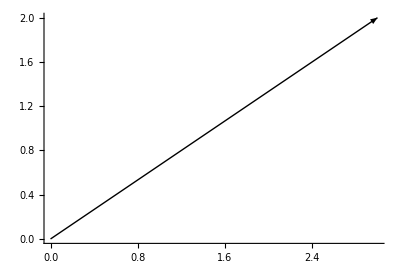

```mathematica
Graphics[Arrow[{{0,0},{3,2}}], Axes->True]
```

igual para 3D

```mathematica
Graphics3D[Arrow[{{0,0,0},{3,2,1}}], Axes->True]
```

-Graphics3D-

para hacer el producto cruz y escalar

```mathematica
y={3,2,5}
```

{3,2,5}

```mathematica
h={5,8,4}
```

{5,8,4}

para el escalar podemos usar

```mathematica
y.h
```

51

```mathematica
Dot[y,h]
```

51

Para el producto cruz, usamos

```mathematica
Cross[y,h]
```

{-32,13,14}

ahora para calcular la norma de un vector usamos

```mathematica
Norm[y]
```

√38

para calcular el angulo entre dos vectores usamos

```mathematica
VectorAngle[y,u]
```

```mathematica
ArcCos[29/38]//N
```

0.70261

para calcular la proyeccion de un vector sobre otro (h sobre y en este caso) usamos

```mathematica
Projection[h,y]
```

{153/38,51/19,255/38}

para ortogonalizar vectores (gram scmidt) usamos

```mathematica
u={2,4,5,7}
```

{2,4,5,7}

```mathematica
v={2,-5,8,9}
```

{2,-5,8,9}

```mathematica
w={3,5,1,2}
```

{3,5,1,2}

```mathematica
{a,b,c}=Orthogonalize[{u,v,w}]
```

{{√(2/47),2 √(2/47),5/(√94),7/(√94)},{7 √(2/412989),-409 √(2/412989),317/(√825978),79 √(3/275326)},{18433/(√356286489),-1234/(√356286489),-1262/(√356286489),-1220 √(3/118762163)}}

y esos son los nuevos vectores






Para crear vectores con un cierto patron usamos

```mathematica
Range[1,5]
```

{1,2,3,4,5}

donde va de 1 a 5, si queremos decirle cuanto avanzar, se lo decimos en un tercer argumento

```mathematica
Range[5,6,0.1]
```

{5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.}

cuando el vector tiene un patron diferente usamos

```mathematica
Table[n^3,{n,1,7}]
```

{1,8,27,64,125,216,343}

donde hicimos que nos de el cubo de los numeros del 1 al 7




Para ver las partes de un vector, hacemos lo siguiente

```mathematica
v={3,5,8,4,1,7}
```

{3,5,8,4,1,7}

```mathematica
v[[5]]
```

1

que es la quinta componente del vector, si ponemos un  negativo cuenta de atars para adelante
para extraer fragmentos mas grandes

```mathematica
v[[2;;4]]
```

{5,8,4}

si queremos, podemos hacer lo anterior usando la función

```mathematica
Part[v,{3,5}]
```

{8,1}

aquí sacó las componentes 3 y 5 NO de la 3 a la 5, esto sería

```mathematica
Part[v,2;;5]
```

```mathematica
{5,8,4,1}
```

## Matrices

una matriz es una lista de listas, entonces se escribe como tal, donde cada lista es una fila

```mathematica
A={{5,7,8},{-3,4,2},{4,7,9}}
```

```mathematica
{{5,7,8},{-3,4,2},{4,7,9}}

B={{1,2,3},{8,4,5},{9,4,6}}
```

{{5,7,8},{-3,4,2},{4,7,9}}

{{1,2,3},{8,4,5},{9,4,6}}

para verla en la forma matricial usamos

```mathematica
A//MatrixForm
```

(5 | 7 | 8
-3 | 4 | 2
4 | 7 | 9)

para hacer operaciones, todo es igual a excepción del producto, si hacemos A*B multiplica componente a componente, para hacer el producto matricial usamos

```mathematica
A.B
```

```mathematica
{{133,70,98},{47,18,23},{141,72,101}}//MatrixForm
```

(133 | 70 | 98
47 | 18 | 23
141 | 72 | 101)

```mathematica
Dot[A,B]
```

```mathematica
{{133,70,98},{47,18,23},{141,72,101}}//MatrixForm
```

(133 | 70 | 98
47 | 18 | 23
141 | 72 | 101)

para elevar una matriz a una potencia, no podemos usar A^5 por ejemplo, esto eleva cada una de las entradas a la 5, lo que hacemos es

```mathematica
MatrixPower[A,5]
```

{{39282,250943,255242},{-6587,-28117,-29262},{39281,250943,255243}}

si elevamos a la -1, obtenemos la inversa de A

Para calcular la inversa podemos usar el anterior metodo o podemos usar

```mathematica
Inverse[A]
```

{{22/59,-7/59,-18/59},{35/59,13/59,-34/59},{-37/59,-7/59,41/59}}

Para calcular determinantes de una matriz usamos

```mathematica
Det[A]
```

59

para calcular la traza de A usamos

```mathematica
Tr[A]
```

18

Para la transpuesta usamos

```mathematica
Transpose[A]//MatrixForm
```

(5 | -3 | 4
7 | 4 | 7
8 | 2 | 9)

para calcular el rango de una matriz

```mathematica
MatrixRank[A]
```

3

Tambien podemos hacer la rduccion por filas para ver el rango asi

```mathematica
RowReduce[A]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

para hacer operaciones de vectores con matrices debemos tener cuidado, si hacemos un A.v, se toma a v como una columna y se hace la operacion, pero si escribes v.A toma a v como una fila y hace la operacion

```mathematica
v={1,8,6}
```

{1,8,6}

```mathematica
A.v
```

{109,41,114}

```mathematica
v.A
```

{5,81,78}

para construir matrices especiales usamos

-Matriz identidad:

```mathematica
IdentityMatrix[4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

-Diagonal con un vector dado (pone el vector en la diagonal):

```mathematica
DiagonalMatrix[v]//MatrixForm
```

(1 | 0 | 0
0 | 8 | 0
0 | 0 | 6)

si en este comando le damos un segundo argumento, esos seran los lugares que desplazara al vector

```mathematica
DiagonalMatrix[v,2]//MatrixForm
```

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

-matriz contante:
los argumentos son, el numero que se repetira y el tamaño de la matriz

```mathematica
ConstantArray[1,{3,2}]//MatrixForm
```

(1 | 1
1 | 1
1 | 1)

-matriz aleatoria:
los argumentos son, el numero maximo que pueden tomar y el tamaño de la matriz

```mathematica
RandomInteger[10,{3,3}]//MatrixForm
```

(5 | 5 | 3
3 | 2 | 2
4 | 8 | 9)

para extraer sub-matrices, hacemos lo siguiente, donde el primer argumento es la fila y el segundo la columna, primero creemos la matriz

```mathematica
A=RandomInteger[10,{10,10}]
%//MatrixForm
```

{{4,2,5,0,10,1,1,1,8,10},{1,8,3,4,4,0,6,3,8,3},{2,2,6,4,5,6,10,7,4,0},{10,1,0,3,5,10,2,7,4,2},{9,6,6,5,10,2,7,2,1,2},{7,2,9,1,3,7,4,1,1,4},{0,4,6,10,3,5,10,0,9,8},{2,10,1,10,9,8,1,5,5,7},{2,1,7,9,10,9,1,5,1,0},{3,6,9,6,4,3,9,9,7,5}}

(4 | 2 | 5 | 0 | 10 | 1 | 1 | 1 | 8 | 10
1 | 8 | 3 | 4 | 4 | 0 | 6 | 3 | 8 | 3
2 | 2 | 6 | 4 | 5 | 6 | 10 | 7 | 4 | 0
10 | 1 | 0 | 3 | 5 | 10 | 2 | 7 | 4 | 2
9 | 6 | 6 | 5 | 10 | 2 | 7 | 2 | 1 | 2
7 | 2 | 9 | 1 | 3 | 7 | 4 | 1 | 1 | 4
0 | 4 | 6 | 10 | 3 | 5 | 10 | 0 | 9 | 8
2 | 10 | 1 | 10 | 9 | 8 | 1 | 5 | 5 | 7
2 | 1 | 7 | 9 | 10 | 9 | 1 | 5 | 1 | 0
3 | 6 | 9 | 6 | 4 | 3 | 9 | 9 | 7 | 5)

ahora para extraer una entrada usamos

```mathematica
A[[2,3]]
```

3

Para una fila

```mathematica
A[[3]]
```

{2,2,6,4,5,6,10,7,4,0}

Para una columna se debe extraer todas las filas, y luego de ellas se saca la columna, asi

```mathematica
A[[All,5]]
```

{10,4,5,5,10,3,3,9,10,4}

para sacar unas filas determinadas se usa

```mathematica
A[[{1,2,4},All]]
```

{{4,2,5,0,10,1,1,1,8,10},{1,8,3,4,4,0,6,3,8,3},{10,1,0,3,5,10,2,7,4,2}}

Para sacar partes de la matriz usamos

```mathematica
Take[A,{2,6},{3,5}]//MatrixForm
```

(3 | 4 | 4
6 | 4 | 5
0 | 3 | 5
6 | 5 | 10
9 | 1 | 3)

saco de la fila 2 a la 6 y de la columna 3 a la 5



Si lo que queremos es borrar usamos

```mathematica
Drop[A,{2,6},{3,5}]//MatrixForm
```

(4 | 2 | 1 | 1 | 1 | 8 | 10
0 | 4 | 5 | 10 | 0 | 9 | 8
2 | 10 | 8 | 1 | 5 | 5 | 7
2 | 1 | 9 | 1 | 5 | 1 | 0
3 | 6 | 3 | 9 | 9 | 7 | 5)

borro de la fila 2 a la 6 y de la columna 3 a la 5

## Sistemas de Ecuaciones

otra manera de resolver es haciendo una matriz asociada y reduciéndola, por ejemplo el sistema 
x+y+4z=25
2x+y    =7
-3x   +z=90
lo podemos resolver asi

```mathematica
A={{1,1,4,25},{2,1,0,7},{-3,0,1,-1}}
```

{{1,1,4,25},{2,1,0,7},{-3,0,1,-1}}

```mathematica
RowReduce[A]//MatrixForm
```

(1 | 0 | 0 | 2
0 | 1 | 0 | 3
0 | 0 | 1 | 5)

otra manera de resolverlo es

```mathematica
A={{1,1,4},{2,1,0},{-3,0,1}}
```

{{1,1,4},{2,1,0},{-3,0,1}}

```mathematica
v={25,7,-1}
```

{25,7,-1}

```mathematica
LinearSolve[A,v]
```

{2,3,5}

sin embargo esta siempre nos da una unica solucion, para saber si esta es la unica vemos el Ker de la matriz, por ejemplo

```mathematica
A={{1,1,4},{2,1,0},{1,1,4}}
```

{{1,1,4},{2,1,0},{1,1,4}}

```mathematica
v={25,7,25}
```

{25,7,25}

```mathematica
LinearSolve[A,v]
```

{-18,43,0}

esta es una de las soluciones porque

```mathematica
NullSpace[A]
```

{{4,-8,1}}

## Estadística

lagunas funciones basicas para estadistica, primero, los datos se introducen como una lista

```mathematica
a={21,22,21,22,23,21,23,23,21,21,21,24,22}
```

{21,22,21,22,23,21,23,23,21,21,21,24,22}

Para saber cuanto da la suma de los datos usamos

```mathematica
Total[a]
```

285

para saber cuantos elementos hay usamos

```mathematica
Length[a]
```

13

para saber la media aritmetica se divide la suma sobre el numero o usamos

```mathematica
Mean[a]
```

285/13

para calcular la mediana (si ordenas al vector, vez cual esta en el medio)

```mathematica
Median[a]
```

22

para calcular la moda se usa

```mathematica
Commonest[a]
```

{21}

para calcular el maximo

```mathematica
Max[a]
```

24

Para calcular el minimo

```mathematica
Min[a]
```

21

Para ver los cuartiles (los elementos que dividen la muestra en 4) usamos

```mathematica
Quartiles[a]
```

{21,22,23}

Para calcular la varianza cuya formula es
(∑(xi-x(media))^2)/(n-1)

```mathematica
Variance[a]
```

14/13

La desviacion estandar es la raiz cuadrada de la anterior varianza, esto es

```mathematica
StandardDeviation[a]
```

√(14/13)

La desviación media calculada como

1/n*∑|xi-x(media)|

se calcula así

```mathematica
MeanDeviation[a]
```

144/169

## Graficos estadisticos

generemos 100 datos aleatorios del 1 al 6

```mathematica
a=RandomInteger[{1,6},100]
```

{3,6,5,1,5,6,1,2,2,5,3,6,4,3,6,3,6,4,5,2,5,1,2,4,4,3,3,2,4,6,5,1,1,5,4,3,6,2,3,3,3,4,6,6,3,3,6,1,3,2,2,1,6,3,5,6,5,3,6,1,3,4,6,1,2,4,2,6,6,2,3,6,6,6,6,3,5,3,4,4,5,5,1,1,6,3,5,1,6,4,4,3,2,2,5,4,4,3,4,2}

para hacer una tabla de frecuencias, primero usamos

```mathematica
Tally[a]//MatrixForm
```

(3 | 22
6 | 22
5 | 14
1 | 12
2 | 14
4 | 16)

el tres salio 22 veces, el 5 14 y así

ahora para hacer la la tabla primero ordenamos con “Sort”

```mathematica
Sort[Tally[a]]
```

{{1,12},{2,14},{3,22},{4,16},{5,14},{6,22}}

luego lo graficamos

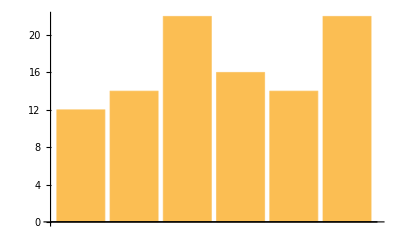

```mathematica
BarChart[Sort[Tally[a]][[All,2]]]
```

usamos el doble corchete para extraer solo la segunda columna

para hacer un diagrama de sectores (como una pizza) usamos

```mathematica
PieChart[Sort[Tally[a]][[All,2]]]
```

-Graphics-

Para hacer un histograma, debemos tener un vector continuo (numeros reales)

```mathematica
a=RandomReal[{0,6},100]
```

{4.49003,1.54164,1.62358,3.12185,2.79462,1.85126,0.463268,5.90698,4.02404,4.70991,1.47914,1.06772,4.84457,4.4621,2.50822,5.31181,3.39796,2.24293,0.458059,5.87873,0.161051,3.30824,0.0662697,2.62301,2.49741,1.2254,1.75803,4.20707,0.0164833,2.03616,3.03283,4.78713,2.01568,2.73229,2.82006,3.46998,1.53429,4.31163,4.45117,1.25452,1.58274,2.37496,5.38726,3.58534,4.01398,1.5869,2.63669,5.96649,4.2414,3.11793,0.544621,4.71706,4.03563,4.98718,2.09668,4.08524,5.47386,5.33122,0.363792,4.20189,0.240135,2.97802,4.37114,3.20498,3.23011,1.83459,0.403779,4.76605,0.389835,3.22748,5.01236,0.825278,5.0676,0.759969,3.0745,2.78317,3.65868,5.37522,2.35518,0.207183,1.42691,4.6184,0.828694,2.13765,4.56822,0.128165,2.48933,3.15801,2.29751,1.09976,0.393711,0.400379,1.42877,1.52732,0.000900174,0.336825,2.73447,0.679785,0.721619,3.3973}

ahora usamos el siguiente comando cuyos argumentos son, el vector, entre corchetes donde empieza, donde termina y la anchura de cada intervalo asi

```mathematica
BinCounts[a,{0,6,2}]
```

{37,33,30}

como cada intervalo tiene un ancho de 2 y hay 6, pues entonces habrá 3 intervalos






para graficar un histograma solo le das el vector y el sistema decide el numero de clases o intervalos

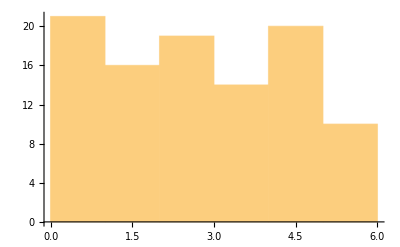

```mathematica
Histogram[a]
```

para hacer un vector aleatorio pero con ciertas especificaciones usamos

```mathematica
a=RandomVariate[NormalDistribution[0,1],10000];
```

el primer comando dice  que haremos un vector aleatorio de cierto tipo, dentro de el ponemos el tipo y el numero de elementos que tendrá. en este caso usamos una distribución gausseana y esta lleva también argumentos, el primero es la media y el segundo es la desviación entandar

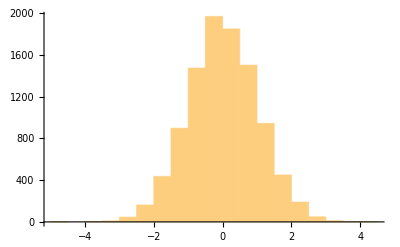

```mathematica
Histogram[a]
```

para hacer un histograma mas suave usamos

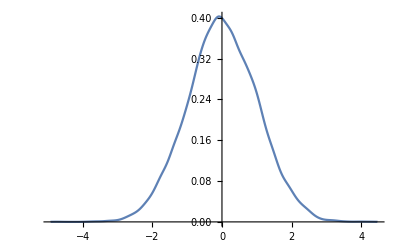

```mathematica
SmoothHistogram[a]
```

para hacer un diagrama de dispersion (graficar puntos) usamos

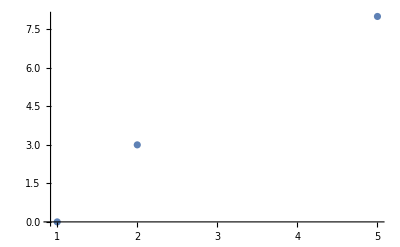

```mathematica
ListPlot[{{1,0},{2,3},{5,8}}]
```

para generar puntos aleatorios lo hacemos como si fuese una matriz

```mathematica
a=RandomReal[{0,2},{100,2}];
```

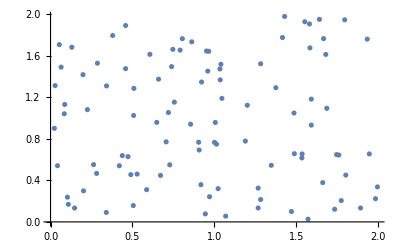

```mathematica
ListPlot[{a}]
```

## Factorizacion de Matrices

una manera de factorizar matrices es con la descomposicion L.U

```mathematica
A={{1,2,1},{4,-1,-3},{-2,1,1}}
```

{{1,2,1},{4,-1,-3},{-2,1,1}}

```mathematica
A//MatrixForm
```

(1 | 2 | 1
4 | -1 | -3
-2 | 1 | 1)

```mathematica
{a,b,c}=LUDecomposition[A]
```

{{{1,2,1},{-2,5,3},{4,-9/5,-8/5}},{1,3,2},0}

el primer elemento es una matriz, el segundo son las operaciones que se hacen en la matriz y el tercero carece de importancia

```mathematica
a//MatrixForm
```

(1 | 2 | 1
-2 | 5 | 3
4 | -9/5 | -8/5)

esta es una convinacion de las matrices L y U

```mathematica
L={{1,0,0},{-2,1,0},{4,-9/5,1}}
```

```mathematica
{{1,0,0},{-2,1,0},{4,-9/5,1}}//MatrixForm
```

(1 | 0 | 0
-2 | 1 | 0
4 | -9/5 | 1)

```mathematica
U={{1,2,1},{0,5,3},{0,0,-8/5}}
```

```mathematica
{{1,2,1},{0,5,3},{0,0,-8/5}}//MatrixForm
```

(1 | 2 | 1
0 | 5 | 3
0 | 0 | -8/5)

Ahora comprobamos que sea correcta

```mathematica
L.U//MatrixForm
```

(1 | 2 | 1
-2 | 1 | 1
4 | -1 | -3)

pero vemos que no son iguales, sino que tiene una permutacion, esto porque no siempre es posible hacer la factorizacion, este es lpo que nos quizo decir la parte b de arriba

```mathematica
b
```

{1,3,2}

nos dice que la fila 1 no cambia, la 2 se cambia por la 3 y la 3 por la 2









también tenemos la factorización QR, donde Q es una matriz ortogonal y R una triangular superior

```mathematica
{Q,R}=QRDecomposition[A];
```

```mathematica
Q//MatrixForm
```

(1/(√21) | 4/(√21) | -2/(√21)
23 √(2/1155) | -√(5/462) | 13/(√2310)
√(2/55) | -√(5/22) | -9/(√110))

```mathematica
OrthogonalMatrixQ[Q]
```

True

## Diagonalizacion de Matrices

Recuerda que para calcular valores propios de una matiz A, se iguala el determinate de la matriz
A- Id(n)X
a 0 y se despeja x, asi

```mathematica
Det[A-IdentityMatrix[3]*x]
```

8+4 x+x^2-x^3

```mathematica
Solve[8+4 x+x^2-x^3==0,x]
```

{{x→Root3.11Root[-8-4 #1-#1^2+#1^3&,1]3.1116942209282468},{x→Root-1.06-1.21 ⅈRoot[-8-4 #1-#1^2+#1^3&,2]-1.0558471104641232},{x→Root-1.06+1.21 ⅈRoot[-8-4 #1-#1^2+#1^3&,3]-1.0558471104641232}}

Asi la Matriz A no tiene valores propios reales






Para encontrar los vectores propios

```mathematica
A={{1,2,1},{2,4,-2},{3,6,-5}}
```

{{1,2,1},{2,4,-2},{3,6,-5}}

```mathematica
Det[A-IdentityMatrix[3]*X]
```

16 X-X^3

```mathematica
Solve[%==0,X]
```

{{X→-4},{X→0},{X→4}}

```mathematica
NullSpace[A-IdentityMatrix[3]*4]
```

{{1,1,1}}

debemos primero ver si es diagonalizable

```mathematica
DiagonalizableMatrixQ[A]
```

True

Para tener el polinomio caracteristico

```mathematica
CharacteristicPolynomial[A,x]
```

16 x-x^3

Para los valores propios

```mathematica
Eigenvalues[A]
```

{-4,4,0}

Y para los vectores propios

```mathematica
Eigenvectors[A]
```

{{-1,1,3},{1,1,1},{-2,1,0}}

## Calculo vectorial

Para graficar un campo vectorial, primero damos el campo, por ejemplo sí es V = yi-xj entonces

```mathematica
V={y,-x}
```

{y,-x}

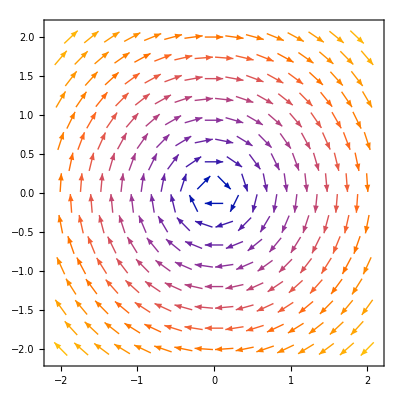

```mathematica
VectorPlot[V,{x,-2,2},{y,-2,2}]
```

donde tanto el dominio como el codominio va de -2 a 2



de igual manera en 3D

```mathematica
VectorPlot3D[{2x+y,4x,5z+y},{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

Para calcular gradiente usamos

```mathematica
f=x^2+y^2+z^2
```

x^2+y^2+z^2

```mathematica
Grad[f,{x,y,z}]
```

{2 x,2 y,2 z}

para el laplaciano

```mathematica
Laplacian[f,{x,y,z}]
```

6

y para el hessiano (como gradiente pero de segundo orden)

```mathematica
D[f,{{x,y,z},2}]
```

{{2,0,0},{0,2,0},{0,0,2}}

Para la divergencia de un campo

```mathematica
V={3(x+y)z,5*x*y*z^3,8*x^2+3z-7y}
```

{3 (x+y) z,5 x y z^3,8 x^2-7 y+3 z}

```mathematica
Div[V,{x,y,z}]
```

3+3 z+5 x z^3

para calcular el rotacional

```mathematica
Curl[V,{x,y,z}]
```

{-7-15 x y z^2,-16 x+3 (x+y),-3 z+5 y z^3}

para otros sistemas de coordenadas, se debe especificar, por ejemplo para calcular el gradiente de una funcion en coordenadas esfericas

```mathematica
Grad[r*Cos[a]*Sin[b],{r,a,b},"Spherical"]
```

{Cos[a] Sin[b],-Sin[a] Sin[b],Cos[b] Cot[a]}

para escribir simbolos presionas escape y escribes el nombre del mismo esc+ theta+espacio

```mathematica
θ
```

## Transformada de Laplace

La transformada de Laplace de un funcion f con variable t es la funcion F con variable s, en otras palabras esta es

F(s) = ∫_0^∞ f(t)*e^(-s*t)ⅆt

por ejemplo para la funcion seno

```mathematica
Integrate[Sin[t]*Exp[-s*t],{t,0,Infinity}]
```

ConditionalExpression[1/(1+s^2), Re[s]>0]

lo que  significa que la parte real de s debe ser mayor que 0


tambien se puede usar el comando, donde la primera es la funcion, la segunda es la primera variable y la tercera es la de la ultima

```mathematica
LaplaceTransform[Sin[t],t,s]
```

1/(1+s^2)

Para la transformada inversa se usa el siguiente comando con el primer argumento como la funcion, el segundo es el de la variable de la transformada y la tercera es la de la funcion sin transformar

```mathematica
InverseLaplaceTransform[1/((s+1)^2*(s+2)),s,t]
```

ⅇ^(-2 t) (1-ⅇ^t+ⅇ^t t)

## Ecuaciones diferenciales

Para esto usamos el siguiente comando, donde le primer argumento es la ecuacion donde se debe especificar de que variable depende, el segundo es la letra de la funcion y el tercero su variable

```mathematica
DSolve[y'[x]==y[x],y,x]
```

{{y→Function[{x},ⅇ^x C[1]]}}

aquí te dice que y es la funcion exponencial multiplicada por cualquier constante

ejemplo

```mathematica
DSolve[y'[x]==2x+3*y[x],y,x]
```

```mathematica
{{y->Function[{x},2 (-1/9-x/3)+ⅇ^(3 x) C[1]]}}//TraditionalForm
```

{{y→({x}↦2 (-x/3-1/9)+1 ⅇ^(3 x))}}

para el caso en el que se nos dan condiciones iniciales, como

y’ =  y       con y(0) = 3

```mathematica
DSolve[{y'[x]==y[x],y[0]==3},y,x]
```

{{y→Function[{x},3 ⅇ^x]}}

y asi para todas las condiciones

```mathematica
DSolve[{y''[x]==y[x],y[3]==4,y'[0]==2},y,x]
```

{{y→Function[{x},(2 ⅇ^-x (2 ⅇ^3-ⅇ^6+ⅇ^(2 x)+2 ⅇ^(3+2 x)))/(1+ⅇ^6)]}}

si queremos usar la funcion directamente la definimos y extraemos, asi

```mathematica
f=DSolve[{y''[x]==y[x],y[3]==4,y'[0]==2},y,x][[1,1,2]]
```

Function[{x},(2 ⅇ^-x (2 ⅇ^3-ⅇ^6+ⅇ^(2 x)+2 ⅇ^(3+2 x)))/(1+ⅇ^6)]

```mathematica
f[5]//N
```

30.205

Para sistemas de ecuaciones diferenciales

```mathematica
DSolve[{x'[t]==t,y'[t]==t^2},{x,y},t]
```

{{x→Function[{t},t^2/2+C[1]],y→Function[{t},t^3/3+C[2]]}}

a veces no se puede resolver de forma precisa y  se debe aproximar, para eso usamos el siguiente comando, solo que aqui debe haber una condicion inicioal y dar un dominio

```mathematica
NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,2*Pi}]
```

{{y→InterpolatingFunction[…]}}

aqui tambien se puede extraer

```mathematica
f=NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,2*Pi}][[1,1,2]]
```

InterpolatingFunction[…]

y ya se puede usar

```mathematica
f[0]
```

1.